```mathematica
(* Some sandboxing before the actual algorithm .... *)
```

```mathematica
Integrate[3/n-4x/n^2,{x,0,n/2}]
```

1

```mathematica
Integrate[3/n-4x/n^2,{x,0,x0}]
```

(3 x0)/n-(2 x0^2)/n^2

```mathematica
((3 x0)/n-(2 x0^2)/n^2)/.{x0->n/8}
```

11/32

```mathematica
((3 x0)/n-(2 x0^2)/n^2)/.{x0->n/4}
```

5/8

```mathematica
((3 x0)/n-(2 x0^2)/n^2)/.{x0->3n/8}
```

27/32

```mathematica
((3 x0)/n-(2 x0^2)/n^2)/.{x0->5n/16}
```

95/128

```mathematica
((3 x0)/n-(2 x0^2)/n^2)/.{x0->7n/16}
```

119/128

```mathematica
MemberQ[{1,2,3,4,5},3]
```

True

```mathematica
Block[
{A},
A={5};
Print[A];
A=AppendTo[A,8];
Print[A];
]
```

{5}

{5,8}

```mathematica
Block[
{k},
For[k=1,k≤5,k++,
If[k==4,Continue[],Print[k]];
]
]
```

1

2

3

5

```mathematica
Binomial[6,3]
```

20

```mathematica
AbsoluteTime[]
```

3.831270689951411×10^9

```mathematica
PDF[ProbabilityDistribution[x,{x,1,2}]]
```

Function[x,Piecewise[{{x, 1<x<2}, {0, True}}],Listable]

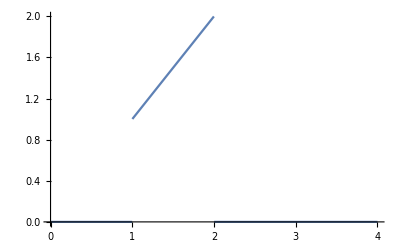

```mathematica
Plot[PDF[ProbabilityDistribution[x,{x,1,2}],x],{x,0,4}]
```

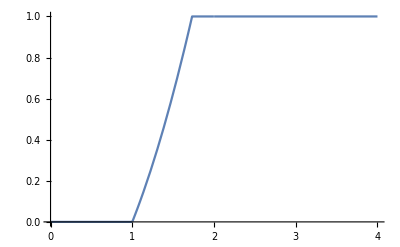

```mathematica
Plot[CDF[ProbabilityDistribution[x,{x,1,2}],x],{x,0,4}]
```

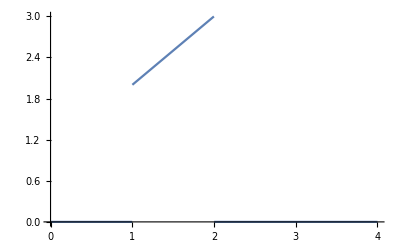

```mathematica
Plot[PDF[ProbabilityDistribution[x+1,{x,1,2}],x],{x,0,4}]
```

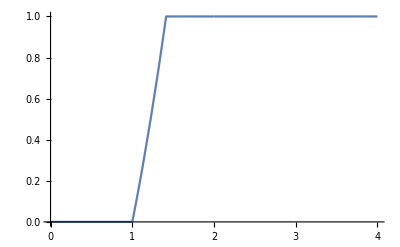

```mathematica
Plot[CDF[ProbabilityDistribution[x+1,{x,1,2}],x],{x,0,4}]
```

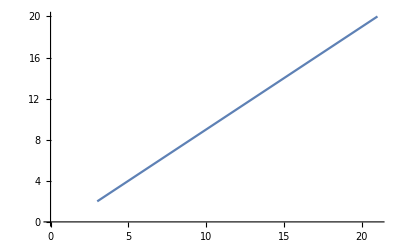

```mathematica
ListLinePlot[Table[PDF[ProbabilityDistribution[x,{x,1,20,1}],x],{x,0,20}]]
```

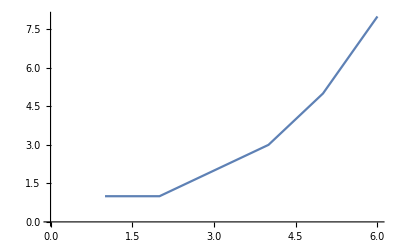

```mathematica
ListLinePlot[{1,1,2,3,5,8}]
```

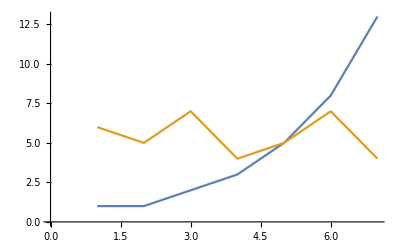

```mathematica
ListLinePlot[{{1,1,2,3,5,8,13},{6,5,7,4,5,7,4}}]
```

```mathematica
RandomVariate[NormalDistribution[]]
```

-0.029414

```mathematica
Mean[RandomVariate[ProbabilityDistribution[x,{x,0,20,1}],30]]//N
```

13.1333

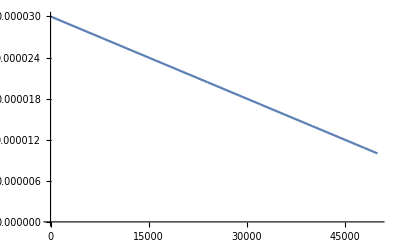

```mathematica
Block[{n=10^5},ListLinePlot[Table[PDF[ProbabilityDistribution[3/n-4x/n^2,{x,0,n/2,1}],x],{x,0,n/2}]]]
```

```mathematica
(* The actual algorithm ...*)
```

```mathematica
Block[
{sum,temp,addtemp,err=0.01,storebox,k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n=50,T=800,P=10^5},
sum=0;
storebox={};
While[True,
k=RandomInteger[{0,n/2}];
If[MemberQ[storebox,k],
Continue[],
AppendTo[storebox,k];
];
Print[k];
temp=1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
addtemp=Binomial[n/2,k](-1)^k temp;
If[Abs[addtemp]/Abs[sum+0.01]<err,
Break[],
sum=sum+addtemp;
]
];
Print[Log[Abs[sum]]];
]
```

7

23

2.237373631175468930715774×10^9

```mathematica
(* can we try some different distribution ... *)
```

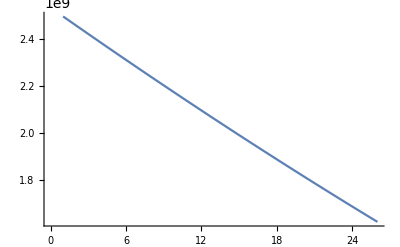

```mathematica
Block[
{k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n=50,T=800,P=10^5},
ListLinePlot[Table[Log[Abs[Binomial[n/2,k](-1)^k (1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]))]],{k,0,n/2}]]
]
```

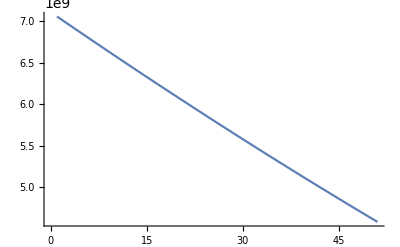

```mathematica
Block[
{k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n=100,T=800,P=10^5},
ListLinePlot[Table[Log[Abs[Binomial[n/2,k](-1)^k (1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]))]],{k,0,n/2}]]
]
```

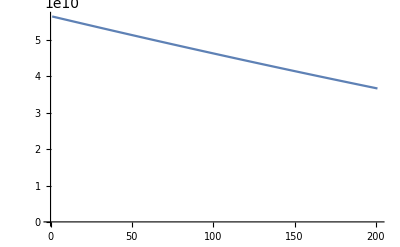

```mathematica
Block[
{k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n=400,T=800,P=10^5},
ListLinePlot[Table[Log[Abs[Binomial[n/2,k](-1)^k (1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]))]],{k,0,n/2}],AxesOrigin->{0,0}]
]
```

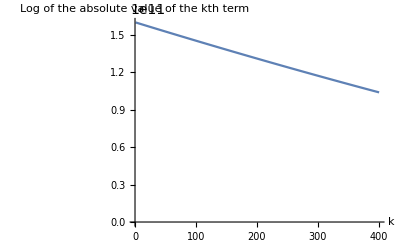

```mathematica
Block[
{k,q=1.6*10^(-19),E0=10^12,kB=1.38*10^(-23),n=800,T=800,P=10^5},
ListLinePlot[Table[Log[Abs[Binomial[n/2,k](-1)^k (1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]))]],{k,0,n/2}],AxesOrigin->{0,0},AxesLabel->{"k","Log of the absolute value of the kth term"}]
]
```

```mathematica
(* I think the uniform distribution works good enough *)
```

```mathematica
Block[
{start,end,sum,temp,addtemp,err=10^(-3),storebox,k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n=50,T=800,P=10^5},
sum=0;
storebox={};
While[True,
k=RandomInteger[{0,n/2}];
If[MemberQ[storebox,k],
Continue[],
AppendTo[storebox,k];
];
Print[k];
temp=1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
addtemp=Binomial[n/2,k](-1)^k temp;
If[Abs[addtemp]/Abs[sum+0.01]<err,
Break[],
sum=sum+addtemp;
]
];
start=AbsoluteTime[];
Print[Log[Abs[sum]]];
end=AbsoluteTime[];
Print["Time consumed by Monte Carlo - ",end-start];
start=AbsoluteTime[];
Print[Sum[Binomial[n/2,k](-1)^k(1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])),{k,0,n/2}]//Abs//Log];
end=AbsoluteTime[];
Print["Time consumed by total time - ",end-start];
]
```

16

5

1

11

2.457349202969358622730718×10^9

Time consumed by Monte Carlo - 0.00013

2.494675622130928685577666×10^9

Time consumed by total time - 1.84885

```mathematica
Block[
{start,end,sum,temp,addtemp,err=10^(-4),storebox,k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n=50,T=800,P=10^5},
sum=0;
storebox={};
While[True,
k=RandomInteger[{0,n/2}];
If[MemberQ[storebox,k],
Continue[],
AppendTo[storebox,k];
];
Print[k];
temp=1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
addtemp=Binomial[n/2,k](-1)^k temp;
If[Abs[addtemp]/Abs[sum+0.01]<err,
Break[],
sum=sum+addtemp;
]
];
start=AbsoluteTime[];
Print[Log[Abs[sum]]];
end=AbsoluteTime[];
Print["Time consumed by Monte Carlo - ",end-start];
start=AbsoluteTime[];
Print[Sum[Binomial[n/2,k](-1)^k(1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])),{k,0,n/2}]//Abs//Log];
end=AbsoluteTime[];
Print["Time consumed by total time - ",end-start];
]
```

7

1

23

2.457349202969358622730718×10^9

Time consumed by Monte Carlo - 0.0002

2.494675622130928685577666×10^9

Time consumed by total time - 1.88949

```mathematica
(* .... So time consumption is definitely saved by Monte Carlo .... let's do a better job by tweaking the probability distribution a little bit .... *)
```

```mathematica
Block[
{start,end,sum,temp,addtemp,err=10^(-4),storebox,k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n=60,T=800,P=10^5,x},
sum=0;
storebox={};
While[True,
k=RandomVariate[ProbabilityDistribution[3/n-4x/n^2,{x,0,n/2,1}]];
If[MemberQ[storebox,k],
Continue[],
AppendTo[storebox,k];
];
Print[k];
temp=1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
addtemp=Binomial[n/2,k](-1)^k temp;
If[Abs[addtemp]/Abs[sum+0.01]<err,
Break[],
sum=sum+addtemp;
]
];
start=AbsoluteTime[];
Print[Log[Abs[sum]]];
end=AbsoluteTime[];
Print["Time consumed by Monte Carlo - ",end-start];
start=AbsoluteTime[];
Print[Sum[Binomial[n/2,k](-1)^k(1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])),{k,0,n/2}]//Abs//Log];
end=AbsoluteTime[];
Print["Time consumed by total time - ",end-start];
]
```

29

11

24

2.838924457511694719284509×10^9

Time consumed by Monte Carlo - 0.00016

3.279336231101161229140605×10^9

Time consumed by total time - 2.45772

```mathematica
Block[
{start,end,sum,temp,addtemp,err=10^(-4),storebox,k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n=100,T=800,P=10^5,x},
sum=0;
storebox={};
start=AbsoluteTime[];
While[True,
k=RandomVariate[ProbabilityDistribution[3/n-4x/n^2,{x,0,n/2,1}]];
If[MemberQ[storebox,k],
Continue[],
AppendTo[storebox,k];
];
Print[k];
temp=1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
addtemp=Binomial[n/2,k](-1)^k temp;
If[Abs[addtemp]/Abs[sum+0.01]<err,
Break[],
sum=sum+addtemp;
]
];
Print[Log[Abs[sum]]];
end=AbsoluteTime[];
Print["Time consumed by Monte Carlo - ",end-start];
start=AbsoluteTime[];
Print[Sum[Binomial[n/2,k](-1)^k(1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])),{k,0,n/2}]//Abs//Log];
end=AbsoluteTime[];
Print["Time consumed by total time - ",end-start];
]
```

11

16

6.481966439990708017070912×10^9

Time consumed by Monte Carlo - 0.34594

7.056007925152977605579168×10^9

Time consumed by total time - 4.238497

```mathematica
Block[
{start,end,sum,temp,addtemp,err=10^(-4),storebox,k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n=200,T=800,P=10^5,x},
sum=0;
storebox={};
While[True,
k=RandomVariate[ProbabilityDistribution[3/n-4x/n^2,{x,0,n/2,1}]];
If[MemberQ[storebox,k],
Continue[],
AppendTo[storebox,k];
];
Print[k];
temp=1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
addtemp=Binomial[n/2,k](-1)^k temp;
If[Abs[addtemp]/Abs[sum+0.01]<err,
Break[],
sum=sum+addtemp;
]
];
start=AbsoluteTime[];
Print[Log[Abs[sum]]];
end=AbsoluteTime[];
Print["Time consumed by Monte Carlo - ",end-start];
start=AbsoluteTime[];
Print[Sum[Binomial[n/2,k](-1)^k(1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])),{k,0,n/2}]//Abs//Log];
end=AbsoluteTime[];
Print["Time consumed by total time - ",end-start];
]
```

55

9

39

1.9287644473976346594070999×10^10

Time consumed by Monte Carlo - 0.00014

1.9957403651817127532248036×10^10

Time consumed by total time - 12.90812

```mathematica
Block[
{sum,temp,addtemp,err=0.01,storebox,k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n=50,T=800,P=10^5},
sum=0;
storebox={};
While[True,
k=RandomInteger[{0,n/2}];
If[MemberQ[storebox,k],
Continue[],
AppendTo[storebox,k];
];
temp=1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
addtemp=Binomial[n/2,k](-1)^k temp;
If[Abs[addtemp]/Abs[sum+0.01]<err,
Break[],
sum=sum+addtemp;
]
];
Print[Log[Abs[sum]]]; (* You got to return this to the function you want to fit it in .... *)
]
```

2.201384147924690004080037×10^9

```mathematica
Block[
{sum,temp,addtemp,err=0.01,storebox,k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n=50,T=800,P=10^5,x},
sum=0;
storebox={};
While[True,
k=RandomVariate[ProbabilityDistribution[3/n-4x/n^2,{x,0,n/2,1}]];
If[MemberQ[storebox,k],
Continue[],
AppendTo[storebox,k];
];
temp=1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
addtemp=Binomial[n/2,k](-1)^k temp;
If[Abs[addtemp]/Abs[sum+0.01]<err,
Break[],
sum=sum+addtemp;
]
];
Print[Log[Abs[sum]]]; (* You got to return this to the function you want to fit it in .... *)
]
```

2.420210827493576229985153×10^9

40 0.13709

40 1.48975

50 0.2349

50 1.87747

60 0.21456

60 2.36793

70 0.16207

70 3.02265

80 0.362846

80 3.848725

90 0.364214

90 4.096401

100 0.18535

100 4.415231

110 0.27955

110 5.277945

120 0.21105

120 7.234025

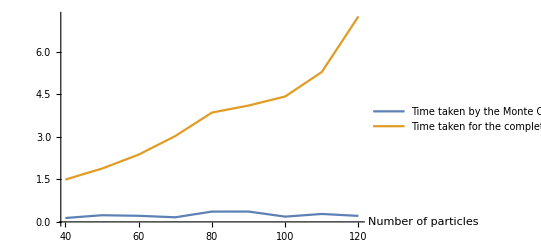

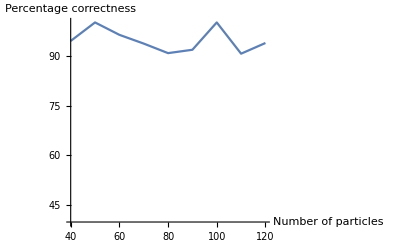

```mathematica
Block[
{start,end,sum,sum1,temp,addtemp,err=10^(-4),storebox,k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n,ActualTime,ExperiTime,sumPercentage,T=800,P=10^5,x},
ActualTime={};
ExperiTime={};
sumPercentage={};
For[n=40,n≤120,n=n+10,
sum=0;
storebox={};
start=AbsoluteTime[];
While[True,
k=RandomVariate[ProbabilityDistribution[3/n-4x/n^2,{x,0,n/2,1}]];
If[MemberQ[storebox,k],
Continue[],
AppendTo[storebox,k];
];
temp=1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
addtemp=Binomial[n/2,k](-1)^k temp;
If[Abs[addtemp]/Abs[sum+0.01]<err,
Break[],
sum=sum+addtemp;
]
];
end=AbsoluteTime[];
AppendTo[ExperiTime,{n,end-start}];
Print[n," ",end-start];
start=AbsoluteTime[];
sum1=Sum[Binomial[n/2,k](-1)^k(1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])),{k,0,n/2}];
end=AbsoluteTime[];
Print[n," ",end-start];
AppendTo[ActualTime,{n,end-start}];
AppendTo[sumPercentage,{n,Abs[Log[sum]]/Abs[Log[sum1]]*100}];
];
Print[ListLinePlot[{ExperiTime,ActualTime},AxesLabel->{"Number of particles"},PlotLegends->{"Time taken by the Monte Carlo algorithm","Time taken for the complete sum"}]];
Print[ListLinePlot[sumPercentage,AxesLabel->{"Number of particles","Percentage correctness"},AxesOrigin->{40,40}]];
]
```

```mathematica
Block[
{T,P,ZGibbs},
ZGibbs[T_,P_]:=Block[
{start,end,sum,temp,addtemp,err=10^(-4),storebox,k,q=1.6*10^(-19),E0=10^12,kB=1.38*10^(-23),n=60,x},
sum=0;
storebox={};
While[True,
k=RandomVariate[ProbabilityDistribution[3/n-4x/n^2,{x,0,n/2,1}]];
If[MemberQ[storebox,k],
Continue[],
AppendTo[storebox,k];
];
temp=1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
addtemp=Binomial[n/2,k](-1)^k temp;
If[Abs[addtemp]/Abs[sum+0.01]<err,
Break[],
sum=sum+addtemp;
]
];
Print[T," ",P," ",Log[Abs[sum]]];
Return[sum];
];
ListPlot3D[Table[Log[Abs[ZGibbs[T,P]]],{T,200,300,10},{P,10^5,2*10^5,10^4}]]
]
```

200 100000 1.2628530596782321583154069×10^10

200 110000 1.235088641840448604592466×10^10

200 120000 1.108768002967378923382844×10^10

200 130000 1.1361163127825692272100378×10^10

200 140000 9.729690890014879607169367×10^9

200 150000 1.004789674041213804231277×10^10

200 160000 1.037017078832927954937719×10^10

200 170000 9.31551458613664275956594×10^9

200 180000 9.777090806967260242946237×10^9

200 190000 9.279407439249062284151176×10^9

200 200000 8.81548114567473124146721×10^9

210 100000 1.1264496003185132524682697×10^10

210 110000 1.031164937342631091125213×10^10

210 120000 1.1261974764617773472895181×10^10

210 130000 1.068405380897604822755832×10^10

210 140000 1.029541187673607003995383×10^10

210 150000 1.007301650042072961443408×10^10

210 160000 8.549968062751550845188083×10^9

210 170000 9.34293408052527540246859×10^9

210 180000 7.621359289249478515477505×10^9

210 190000 7.845988827825492975277023×10^9

210 200000 8.287365632341624999137209×10^9

220 100000 9.20795969943261672979755×10^9

220 110000 1.1228078602493844070278689×10^10

220 120000 1.088585615310534153128736×10^10

220 130000 9.557126562908362819950808×10^9

220 140000 8.60504143888021740172493×10^9

220 150000 9.49420772389661340701413×10^9

220 160000 9.076118349816854900574627×10^9

220 170000 8.918255278721933230865552×10^9

220 180000 8.88826440953344779743051×10^9

220 190000 7.592653502597145499724324×10^9

220 200000 7.705201855131139794962247×10^9

230 100000 1.1264103481076064251829872×10^10

230 110000 9.806338582173024168296747×10^9

230 120000 1.02826726495676408432809×10^10

230 130000 7.383183059097548466248509×10^9

230 140000 9.51990505097719942248561×10^9

230 150000 7.841627978786023126335493×10^9

230 160000 8.240126334772581053184833×10^9

230 170000 8.100447524513398599358163×10^9

230 180000 8.080289628455835172310608×10^9

230 190000 7.966694965671241604703654×10^9

230 200000 7.175392630974218448694263×10^9

240 100000 9.98873408443729927377287×10^9

240 110000 9.777846266368154789997029×10^9

240 120000 9.978701510136996034008279×10^9

240 130000 7.513138149368541656244627×10^9

240 140000 9.008485447384512147338109×10^9

240 150000 7.726572957472432936484467×10^9

240 160000 7.584410472206473970270607×10^9

240 170000 8.383786262953160145950011×10^9

240 180000 7.053363874082339532172097×10^9

240 190000 7.634749360429108181325581×10^9

240 200000 6.146581409618722860426955×10^9

250 100000 9.462176715129076575262353×10^9

250 110000 8.90127354599238844086954×10^9

250 120000 6.430654067804633826669184×10^9

250 130000 9.088930590319650820473415×10^9

250 140000 8.758312681953116236769023×10^9

250 150000 7.315668715348170744088268×10^9

250 160000 6.790284741394685764442876×10^9

250 170000 7.748512834357702475748654×10^9

250 180000 6.493615589416439638423317×10^9

250 190000 7.423526039163321319288929×10^9

250 200000 7.235558172754655279206197×10^9

260 100000 9.964399284168395214466834×10^9

260 110000 9.143686408000890560455571×10^9

260 120000 8.867860486635806287388821×10^9

260 130000 6.531277372824515357952734×10^9

260 140000 8.315525062182129420729867×10^9

260 150000 8.135898026865512025617154×10^9

260 160000 7.977054552850716396830355×10^9

260 170000 6.607571372756439334205142×10^9

260 180000 7.520839182293610612300463×10^9

260 190000 7.228935147110644583214232×10^9

260 200000 6.176684826884211432208375×10^9

270 100000 9.716550965619174789943126×10^9

270 110000 9.033726418700776409329602×10^9

270 120000 8.213096434640629330582259×10^9

270 130000 7.68414635111412327157273×10^9

270 140000 8.007542668714467714598009×10^9

270 150000 7.637890586203245080462909×10^9

270 160000 7.206543966589124256753806×10^9

270 170000 6.719591110037033425504273×10^9

270 180000 6.705965239145377637329381×10^9

270 190000 6.356096888475988310061841×10^9

270 200000 5.62353276853985386706965×10^9

280 100000 9.252656509528463787783102×10^9

280 110000 8.055206772811701095555376×10^9

280 120000 7.302827031317220014383094×10^9

280 130000 7.310697196149418633123466×10^9

280 140000 7.428972420781690832475494×10^9

280 150000 7.459734734295314834908943×10^9

280 160000 7.040005480462098957879719×10^9

280 170000 5.714488827855442415125059×10^9

280 180000 5.962733384080911880984458×10^9

280 190000 6.211362465986068912159697×10^9

280 200000 5.040005590344621487111855×10^9

290 100000 9.04644403249506917939851×10^9

290 110000 8.517852839003950610076011×10^9

290 120000 7.247770658945491086291462×10^9

290 130000 7.540868092827856594897554×10^9

290 140000 7.360728712564840799793181×10^9

290 150000 7.202502517125006464302844×10^9

290 160000 6.44871351362933713047627×10^9

290 170000 6.256171064058040808400967×10^9

290 180000 6.408505658436986782804089×10^9

290 190000 6.157097093705424631658207×10^9

290 200000 6.23755020886205815796387×10^9

300 100000 6.853036425998378692734693×10^9

300 110000 6.824492939224214615419069×10^9

300 120000 7.982961294956487497479695×10^9

300 130000 7.478837798346010836623791×10^9

300 140000 6.575113196668925202751958×10^9

300 150000 6.874101571416541583622405×10^9

300 160000 5.259237697444714321121455×10^9

300 170000 5.886367249847493289730497×10^9

300 180000 5.798704839164543702757775×10^9

300 190000 5.720487243812805666175691×10^9

300 200000 5.650481478426676066640891×10^9

-Graphics3D-

```mathematica
Block[
{T,P,ZGibbs,kGibbs},
ZGibbs[T_,P_]:=Block[
{start,end,sum,temp,addtemp,err=10^(-4),storebox,k,q=1.6*10^(-19),E0=10^12,kB=1.38*10^(-23),n=60,x},
sum=0;
storebox={};
While[True,
k=RandomVariate[ProbabilityDistribution[3/n-4x/n^2,{x,0,n/2,1}]];
If[MemberQ[storebox,k],
Continue[],
AppendTo[storebox,k];
];
temp=1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
addtemp=Binomial[n/2,k](-1)^k temp;
If[Abs[addtemp]/Abs[sum+0.01]<err,
Break[],
sum=sum+addtemp;
]
];
Return[sum];
];
kGibbs={};
For[
T=200,T≤300,T=T+10,
For[
P=10^5,P=2*10^5,P=P+10^4,
Print[{T,P,Log[Abs[ZGibbs[T,P]]]}];
AppendTo[kGibbs,{T,P,Log[Abs[ZGibbs[T,P]]]}];
]
];
ListPlot3D[kGibbs,AxesLabel->{"T","P","-G/kB/T"}]
]
```

ListPlot3D::arrayerr: {} must be a valid array or a list of valid arrays.

ListPlot3D[{},AxesLabel→{T,P,-G/kB/T}]

40 1.429840999359468720587493×10^9 1.785044594966824251469089×10^9

60 3.116743527908318574449867×10^9 3.279336231101161229140605×10^9

80 4.81406136592916064943461×10^9 5.048868334268218004808176×10^9

100 6.897844620091504287457588×10^9 7.056007925152977605579168×10^9

120 8.758546423399591106865277×10^9 9.275363219598408917837271×10^9

140 1.015837727579976659120458×10^10 1.1688293462972835657971962×10^10

160 1.4280355705058408963035486×10^10 1.4280355705058408963035486×10^10

180 1.4751483294590670489602307×10^10 1.7039930028151634392448818×10^10

200 1.4146687131819389314620269×10^10 1.9957403651817127532248036×10^10

220 2.1626325350107188341668297×10^10 2.3024651616662169649211692×10^10

240 2.4853384613261731093885553×10^10 2.6234688249211990286672182×10^10

260 2.131957219007037581793433×10^10 2.9581423299732795503203764×10^10

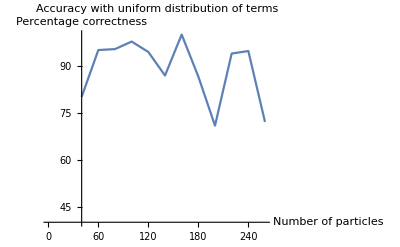

```mathematica
Block[
{start,end,sum,sum1,temp,addtemp,err=10^(-4),storebox,k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n,ActualTime,ExperiTime,sumPercentage,T=800,P=10^5,x},
ActualTime={};
ExperiTime={};
sumPercentage={};
For[n=40,n≤260,n=n+20,
sum=0;
storebox={};
While[True,
k=RandomInteger[{0,n/2}];
If[MemberQ[storebox,k],
Continue[],
AppendTo[storebox,k];
];
temp=1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
addtemp=Binomial[n/2,k](-1)^k temp;
If[Abs[addtemp]/Abs[sum+0.01]<err,
Break[],
sum=sum+addtemp;
]
];
sum1=Sum[Binomial[n/2,k](-1)^k(1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])),{k,0,n/2}];
Print[n," ",Abs[Log[sum]]," ",Abs[Log[sum1]]];
AppendTo[sumPercentage,{n,Abs[Log[sum]]/Abs[Log[sum1]]*100}];
];
Print[ListLinePlot[sumPercentage,AxesLabel->{"Number of particles","Percentage correctness"},PlotLabel->"Accuracy with uniform distribution of terms",AxesOrigin->{40,40}]];
]
```

40 1.718525567560827088641109×10^9 1.785044594966824251469089×10^9

60 3.036486547920689627239374×10^9 3.279336231101161229140605×10^9

80 4.954498521481022859534317×10^9 5.048868334268218004808176×10^9

100 7.003154080241361148150897×10^9 7.056007925152977605579168×10^9

120 8.532039426160311533589215×10^9 9.275363219598408917837271×10^9

140 1.100632882175446068896818×10^10 1.1688293462972835657971962×10^10

160 1.4213468871032097144892634×10^10 1.4280355705058408963035486×10^10

180 1.6125317370455163115503906×10^10 1.7039930028151634392448818×10^10

200 1.9733304393515768157480497×10^10 1.9957403651817127532248036×10^10

220 1.8698734823382034189826618×10^10 2.3024651616662169649211692×10^10

240 2.566290190579300660469142×10^10 2.6234688249211990286672182×10^10

260 2.7390784893294089461539142×10^10 2.9581423299732795503203764×10^10

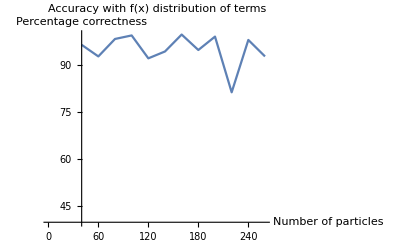

```mathematica
Block[
{start,end,sum,sum1,temp,addtemp,err=10^(-4),storebox,k,q=1.6*10^(-19),L=10^(-3),E0=10^12,kB=1.38*10^(-23),n,ActualTime,ExperiTime,sumPercentage,T=800,P=10^5,x},
ActualTime={};
ExperiTime={};
sumPercentage={};
For[n=40,n≤260,n=n+20,
sum=0;
storebox={};
While[True,
k=RandomVariate[ProbabilityDistribution[3/n-4x/n^2,{x,0,n/2,1}]];
If[MemberQ[storebox,k],
Continue[],
AppendTo[storebox,k];
];
temp=1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
temp=temp+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P]);
addtemp=Binomial[n/2,k](-1)^k temp;
If[Abs[addtemp]/Abs[sum+0.01]<err,
Break[],
sum=sum+addtemp;
]
];
sum1=Sum[Binomial[n/2,k](-1)^k(1/48 (q E0/kB/T)^2 (kB T/P)^(2/3)Gamma[(n+5)/3]((2n+k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k)^2 HypergeometricPFQ[{(n+5)/3},{4/3,5/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/12(q E0/kB/T)(kB T/P)^(1/3)Gamma[(n+4)/3](-(2n+k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+(2n-k) HypergeometricPFQ[{(n+4)/3},{2/3,4/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])+1/6Gamma[(n+3)/3]( HypergeometricPFQ[{(n+3)/3},{1/3,2/3},-(q E0)^3 (2n+k)^3/216/(kB T)^2/P]+HypergeometricPFQ[{(n+3)/3},{1/3,2/3},(q E0)^3 (2n-k)^3/216/(kB T)^2/P])),{k,0,n/2}];
Print[n," ",Abs[Log[sum]]," ",Abs[Log[sum1]]];
AppendTo[sumPercentage,{n,Abs[Log[sum]]/Abs[Log[sum1]]*100}];
];
Print[ListLinePlot[sumPercentage,AxesLabel->{"Number of particles","Percentage correctness"},PlotLabel->"Accuracy with f(x) distribution of terms",AxesOrigin->{40,40}]];
]
```